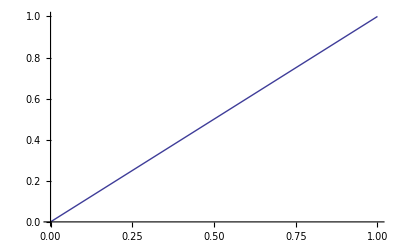
n_max
V_0
-Graphics-

```mathematica
Panel[
Column[{
Row[{"n_max",Slider[Dynamic[nmax],{1,20,1}],Dynamic[nmax]}],
Row[{"V_0",Slider[Dynamic[V0],{0.1,5,0.1}],Dynamic[V0]}],
Plot[x,{x,0,1}]
}]
]
```

```mathematica
Panel[
Grid[{{"n_max",Slider[Dynamic[nmax],{1,20,1}],Dynamic[nmax]},{"V_0",Slider[Dynamic[V0],{0.1,5,0.1}],Dynamic[V0]},{"",Dynamic[Plot3D[Evaluate[(4V0)/π Sum[ⅇ^(-n π x)Sin[n π y],{n,1,nmax}]],{x,0,2},{y,0,1},PlotRange->Full]]}}]
]
```

n_max |  | 
V_0 |  | 
 |  |